# Force Calculation for Spheroid case -

This Mathematica file deals with calculation of force when applied magnetic field is displaced in z direction only. This file is cross referenced with Section E(e) my notes. Please refer to notes for detailed explanations.

## In Cartesian Coordinates -

```mathematica
Clear["Global`*"]
```

```mathematica
R = Symbol["R"];
ϵ = Symbol["ϵ"];
```

## Definition of Spheroid-

```mathematica
vsph[θ_, ϕ_]= (R-ϵ Cos[2 θ])er[θ, ϕ]
```

(R-ϵ Cos[2 θ]) er[θ,ϕ]

## Normal vector Calculation for Spheroid (in Spherical Coordinates)-

This section is described in detail in the file - “Normal Vector to surface of Spheroid.nb” or Section B(b) of my notes. Please refer to them in case of any detailed explanations. The unit normal vector is not used throughout this calculation. We have used the normal vector only.

```mathematica
Clear["Global`*"]
vsph[θ_, ϕ_]= (R-ϵ Cos[2 θ])er[θ, ϕ];
vsphθ[ θ_, ϕ_]:= FullSimplify[D[vsph[ θ, ϕ], {θ}]];
vsphϕ[ θ_, ϕ_]:= FullSimplify[D[vsph[ θ, ϕ], {ϕ}]];
finvsphθ[ θ_, ϕ_]=Collect[vsphθ[θ, ϕ], {er[θ,ϕ], Derivative[1,0][er][θ,ϕ], Derivative[0,1][er][θ,ϕ]}, Simplify]/. {Derivative[1,0][er][θ,ϕ]->eθ[θ,ϕ], Derivative[0,1][er][θ,ϕ]-> Sin[θ]eϕ[θ,ϕ]};
finvsphϕ[ θ_, ϕ_]=Collect[vsphϕ[θ, ϕ], {er[θ,ϕ], Derivative[1,0][er][θ,ϕ], Derivative[0,1][er][θ,ϕ]}, Simplify]/. {Derivative[1,0][er][θ,ϕ]->eθ[θ,ϕ], Derivative[0,1][er][θ,ϕ]-> Sin[θ]eϕ[θ,ϕ]};
eθ[θ,ϕ] = {0, 1, 0};
er[θ,ϕ] = {1, 0, 0};
eϕ[θ,ϕ] = {0, 0, 1};
finalvsphθ[ θ_, ϕ_]=finvsphθ[ θ, ϕ];
finalvsphϕ[ θ_, ϕ_]=finvsphϕ[ θ, ϕ];
nvsph[ θ_, ϕ_]:= Cross[finalvsphθ[θ, ϕ], finalvsphϕ[θ, ϕ]];
normal[θ_, ϕ_] =nvsph[ θ, ϕ]//FullSimplify(*Eqn 1e/ 12b*)
```

{(R-ϵ Cos[2 θ])^2 Sin[θ],4 ϵ Cos[θ] (-R+ϵ Cos[2 θ]) Sin[θ]^2,0}

```mathematica
normalcolvector[θ_, ϕ_] = Transpose[normal[θ, ϕ]]
```

{(R-ϵ Cos[2 θ])^2 Sin[θ],4 ϵ Cos[θ] (-R+ϵ Cos[2 θ]) Sin[θ]^2,0}

## Normal vector in Cartesian Coordinates -

```mathematica
SphToCar = {{Sin[θ]Cos[ϕ],Cos[θ]Cos[ϕ], -Sin[ϕ]},{Sin[θ]Sin[ϕ], Cos[θ]Sin[ϕ] , Cos[ϕ]},{Cos[θ], -Sin[θ], 0}}(*Eqn. 2e*)
```

{{Cos[ϕ] Sin[θ],Cos[θ] Cos[ϕ],-Sin[ϕ]},{Sin[θ] Sin[ϕ],Cos[θ] Sin[ϕ],Cos[ϕ]},{Cos[θ],-Sin[θ],0}}

```mathematica
MatrixForm[SphToCar](*Eqn. 2e*)
```

(Cos[ϕ] Sin[θ] | Cos[θ] Cos[ϕ] | -Sin[ϕ]
Sin[θ] Sin[ϕ] | Cos[θ] Sin[ϕ] | Cos[ϕ]
Cos[θ] | -Sin[θ] | 0)

```mathematica
normalCart[θ_, ϕ_]=FullSimplify[Dot[SphToCar, normalcolvector[θ, ϕ]]]/.{ϵ->R s}(*Eqn. 3e*)
```

{(R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Cos[ϕ] Sin[θ]^2,(R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Sin[θ]^2 Sin[ϕ],Cos[θ] (R+2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Sin[θ]}

(*Eqn. 3e*)

```mathematica
nx[θ_, ϕ_] =normalCart[θ,ϕ][[1]]
ny[θ_, ϕ_] =normalCart[θ,ϕ][[2]]
nz[θ_, ϕ_] =normalCart[θ,ϕ][[3]]
```

(R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Cos[ϕ] Sin[θ]^2

(R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Sin[θ]^2 Sin[ϕ]

Cos[θ] (R+2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Sin[θ]

## Area Element for the spheroid -

Refer notes for its detailed explanations, (*Eqn. 4e-7e*)

Reference for using the area element as normal vector - Marsden Pg - 384 (Area of a parametrized surface)

#### (*Eqn. 7e*)

```mathematica
Ax[θ_, ϕ_]= nx[θ, ϕ];(*Eqn.7e*)
Ay[θ_, ϕ_]= ny[θ, ϕ];(*Eqn.7e*)
Az[θ_, ϕ_]= nz[θ, ϕ];(*Eqn.7e*)
```

```mathematica
FullSimplify[Integrate[Norm[normalCart[θ, ϕ]], {θ, 0, π}, {ϕ, 0, 2π}]]
```

$Aborted

## Bout at surface of the Spheroid in Spherical coordinates can be written as -

```mathematica
BoutSpheroid[θ_, ϕ_]={2 bz s Cos[θ] (3 dz+5 R Cos[θ]) Sin[θ]^2,-1/140 bz (25 R (-14+25 s) Cos[θ]+42 dz (-5+6 s+10 s Cos[2 θ])+525 R s Cos[3 θ]) Sin[θ],0}(*Eqn. 8e/42d*)
```

{2 bz s Cos[θ] (3 dz+5 R Cos[θ]) Sin[θ]^2,-1/140 bz (25 R (-14+25 s) Cos[θ]+42 dz (-5+6 s+10 s Cos[2 θ])+525 R s Cos[3 θ]) Sin[θ],0}

### Passed the test for Sphere case

```mathematica
FullSimplify[BoutSpheroid[θ, ϕ]/.s->0]
```

{0,1/2 bz (3 dz+5 R Cos[θ]) Sin[θ],0}

## Bout at surface of the Spheroid in Cartesian coordinates -

```mathematica
Boutr[θ_, ϕ_]=BoutSpheroid[θ, ϕ][[1]]
Boutθ[θ_, ϕ_]=BoutSpheroid[θ, ϕ][[2]]
Boutϕ[θ_, ϕ_]=BoutSpheroid[θ, ϕ][[3]]
```

2 bz s Cos[θ] (3 dz+5 R Cos[θ]) Sin[θ]^2

-1/140 bz (25 R (-14+25 s) Cos[θ]+42 dz (-5+6 s+10 s Cos[2 θ])+525 R s Cos[3 θ]) Sin[θ]

0

```mathematica
BoutCart[θ_, ϕ_]=FullSimplify[Dot[SphToCar, BoutSpheroid[θ, ϕ]]](*Eqn. 9e*)
```

{1/280 bz (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) Cos[ϕ] Sin[2 θ],1/280 bz (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) Sin[2 θ] Sin[ϕ],1/140 bz (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ]) Sin[θ]^2}

```mathematica
Bout2[θ_, ϕ_]= Collect[Expand[Refine[Norm[BoutCart[θ, ϕ]]^2, {Element[BoutCart[θ, ϕ][[1]], Reals], Element[BoutCart[θ, ϕ][[2]], Reals], Element[BoutCart[θ, ϕ][[3]], Reals]}]], {s}](*Eqn. 10e*)
```

9/4 bz^2 dz^2 Sin[θ]^4+15/2 bz^2 dz R Cos[θ] Sin[θ]^4+25/4 bz^2 R^2 Cos[θ]^2 Sin[θ]^4+9/16 bz^2 dz^2 Cos[ϕ]^2 Sin[2 θ]^2+15/8 bz^2 dz R Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2+25/16 bz^2 R^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2+9/16 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2+15/8 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2+25/16 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2+s (-72/5 bz^2 dz^2 Sin[θ]^4-1677/28 bz^2 dz R Cos[θ] Sin[θ]^4-1675/28 bz^2 R^2 Cos[θ]^2 Sin[θ]^4-18 bz^2 dz^2 Cos[2 θ] Sin[θ]^4-30 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4-75/4 bz^2 dz R Cos[3 θ] Sin[θ]^4-125/4 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4+9/10 bz^2 dz^2 Cos[ϕ]^2 Sin[2 θ]^2+3/112 bz^2 dz R Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2-275/112 bz^2 R^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-9/2 bz^2 dz^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-15/2 bz^2 dz R Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-75/16 bz^2 dz R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2-125/16 bz^2 R^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+9/10 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2+3/112 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2-275/112 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-9/2 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-15/2 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-75/16 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2-125/16 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)+s^2 (576/25 bz^2 dz^2 Sin[θ]^4+804/7 bz^2 dz R Cos[θ] Sin[θ]^4+112225/784 bz^2 R^2 Cos[θ]^2 Sin[θ]^4+288/5 bz^2 dz^2 Cos[2 θ] Sin[θ]^4+1005/7 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4+36 bz^2 dz^2 Cos[2 θ]^2 Sin[θ]^4+60 bz^2 dz R Cos[3 θ] Sin[θ]^4+8375/56 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4+75 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[θ]^4+625/16 bz^2 R^2 Cos[3 θ]^2 Sin[θ]^4+9/25 bz^2 dz^2 Cos[ϕ]^2 Sin[2 θ]^2-33/28 bz^2 dz R Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2+(3025 bz^2 R^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2)/3136-18/5 bz^2 dz^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+165/28 bz^2 dz R Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+9 bz^2 dz^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-15/4 bz^2 dz R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+1375/224 bz^2 R^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+75/4 bz^2 dz R Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+625/64 bz^2 R^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2+9/25 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2-33/28 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2+(3025 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/3136-18/5 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+165/28 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+9 bz^2 dz^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-15/4 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+1375/224 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+75/4 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+625/64 bz^2 R^2 Cos[3 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)

### Different components of Magnetic field outside the sphere - Bout (*Eqn. 11e*)

```mathematica
Bx[θ_, ϕ_]= BoutCart[θ, ϕ][[1]];(*Eqn.11e*)
By[θ_, ϕ_]= BoutCart[θ, ϕ][[2]];(*Eqn.11e*)
Bz[θ_, ϕ_]= BoutCart[θ, ϕ][[3]];(*Eqn.11e*)
```

### Square of different components of Magnetic field outside the sphere - Bout

```mathematica
Bx2[θ_, ϕ_]= Collect[Expand[(Bx[θ, ϕ])^2],dz]
By2[θ_, ϕ_]=(By[θ, ϕ])^2
Bz2[θ_, ϕ_]= (Bz[θ, ϕ])^2
```

25/16 bz^2 R^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-275/112 bz^2 R^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2+(3025 bz^2 R^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2)/3136-125/16 bz^2 R^2 s Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+1375/224 bz^2 R^2 s^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+625/64 bz^2 R^2 s^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2+dz^2 (9/16 bz^2 Cos[ϕ]^2 Sin[2 θ]^2+9/10 bz^2 s Cos[ϕ]^2 Sin[2 θ]^2+9/25 bz^2 s^2 Cos[ϕ]^2 Sin[2 θ]^2-9/2 bz^2 s Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-18/5 bz^2 s^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+9 bz^2 s^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2)+dz (15/8 bz^2 R Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2+3/112 bz^2 R s Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2-33/28 bz^2 R s^2 Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2-15/2 bz^2 R s Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+165/28 bz^2 R s^2 Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-75/16 bz^2 R s Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2-15/4 bz^2 R s^2 Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+75/4 bz^2 R s^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2)

(bz^2 (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ])^2 Sin[2 θ]^2 Sin[ϕ]^2)/78400

(bz^2 (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ])^2 Sin[θ]^4)/19600

## Calculating the Maxwell Stress Tensors

### For x component of the force -

```mathematica
Txx[θ_, ϕ_]= 1/μ(Bx2[θ, ϕ]-1/2 Bout2[θ, ϕ])(*Eqn.16e*)
```

1/μ(25/16 bz^2 R^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-275/112 bz^2 R^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2+(3025 bz^2 R^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2)/3136-125/16 bz^2 R^2 s Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+1375/224 bz^2 R^2 s^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+625/64 bz^2 R^2 s^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2+dz^2 (9/16 bz^2 Cos[ϕ]^2 Sin[2 θ]^2+9/10 bz^2 s Cos[ϕ]^2 Sin[2 θ]^2+9/25 bz^2 s^2 Cos[ϕ]^2 Sin[2 θ]^2-9/2 bz^2 s Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-18/5 bz^2 s^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+9 bz^2 s^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2)+dz (15/8 bz^2 R Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2+3/112 bz^2 R s Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2-33/28 bz^2 R s^2 Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2-15/2 bz^2 R s Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+165/28 bz^2 R s^2 Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-75/16 bz^2 R s Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2-15/4 bz^2 R s^2 Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+75/4 bz^2 R s^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2)+1/2 (-9/4 bz^2 dz^2 Sin[θ]^4-15/2 bz^2 dz R Cos[θ] Sin[θ]^4-25/4 bz^2 R^2 Cos[θ]^2 Sin[θ]^4-9/16 bz^2 dz^2 Cos[ϕ]^2 Sin[2 θ]^2-15/8 bz^2 dz R Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2-25/16 bz^2 R^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-9/16 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2-15/8 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2-25/16 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-s (-72/5 bz^2 dz^2 Sin[θ]^4-1677/28 bz^2 dz R Cos[θ] Sin[θ]^4-1675/28 bz^2 R^2 Cos[θ]^2 Sin[θ]^4-18 bz^2 dz^2 Cos[2 θ] Sin[θ]^4-30 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4-75/4 bz^2 dz R Cos[3 θ] Sin[θ]^4-125/4 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4+9/10 bz^2 dz^2 Cos[ϕ]^2 Sin[2 θ]^2+3/112 bz^2 dz R Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2-275/112 bz^2 R^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-9/2 bz^2 dz^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-15/2 bz^2 dz R Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-75/16 bz^2 dz R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2-125/16 bz^2 R^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+9/10 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2+3/112 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2-275/112 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-9/2 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-15/2 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-75/16 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2-125/16 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)-s^2 (576/25 bz^2 dz^2 Sin[θ]^4+804/7 bz^2 dz R Cos[θ] Sin[θ]^4+112225/784 bz^2 R^2 Cos[θ]^2 Sin[θ]^4+288/5 bz^2 dz^2 Cos[2 θ] Sin[θ]^4+1005/7 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4+36 bz^2 dz^2 Cos[2 θ]^2 Sin[θ]^4+60 bz^2 dz R Cos[3 θ] Sin[θ]^4+8375/56 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4+75 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[θ]^4+625/16 bz^2 R^2 Cos[3 θ]^2 Sin[θ]^4+9/25 bz^2 dz^2 Cos[ϕ]^2 Sin[2 θ]^2-33/28 bz^2 dz R Cos[θ] Cos[ϕ]^2 Sin[2 θ]^2+(3025 bz^2 R^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ]^2)/3136-18/5 bz^2 dz^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+165/28 bz^2 dz R Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+9 bz^2 dz^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-15/4 bz^2 dz R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+1375/224 bz^2 R^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+75/4 bz^2 dz R Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[2 θ]^2+625/64 bz^2 R^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2+9/25 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2-33/28 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2+(3025 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/3136-18/5 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+165/28 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+9 bz^2 dz^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-15/4 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+1375/224 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+75/4 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+625/64 bz^2 R^2 Cos[3 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)))

```mathematica
TxxAx[θ_, ϕ_] =FullSimplify[Txx[θ, ϕ]Ax[θ, ϕ]]
```

1/(1254400 μ)bz^2 R^2 (2+s (-4+3 s)+4 (-2+s) s Cos[2 θ]+3 s^2 Cos[4 θ]) ((-7056 dz^2 (25+4 s (-15+34 s))-625 R^2 (-196+s (112+915 s))-8400 dz R (-35+s (-18+253 s)) Cos[θ]+4 (-1764 dz^2 (15+2 s) (-5+6 s)+625 R^2 (196+s (-553+191 s))) Cos[2 θ]+4200 dz R (210+s (-907+670 s)) Cos[3 θ]+20 (21168 dz^2 s (-5+6 s)+125 R^2 (147+2 s (-630+713 s))) Cos[4 θ]+21000 dz R s (-189+346 s) Cos[5 θ]+700 s (3024 dz^2 s+125 R^2 (-21+55 s)) Cos[6 θ]+4410000 dz R s^2 Cos[7 θ]+2296875 R^2 s^2 Cos[8 θ]) Cos[ϕ]+8 Cos[θ]^2 (25 R (-14+11 s) Cos[θ]+42 dz (-5-4 s+20 s Cos[2 θ])+875 R s Cos[3 θ])^2 Cos[3 ϕ]) Sin[θ]^4

#### Integrating the first part of the Integral for x component of force -

```mathematica
Fx1=Integrate[TxxAx[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}](*Eqn.19e Part 1*)
```

0

### Calculating the second part of x component of force

```mathematica
Txy[θ_, ϕ_]= FullSimplify[ 1/μ(Bx[θ, ϕ]By[θ, ϕ])](*Eqn.17e*)
```

(bz^2 (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ])^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(78400 μ)

```mathematica
TxyAy[θ_, ϕ_]=Txy[θ, ϕ]Ay[θ, ϕ]
```

1/(78400 μ)bz^2 (R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ])^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2

#### Integrating the second part of the Integral for x component of force -

```mathematica
Fx2=Integrate[TxyAy[θ,ϕ], {θ, 0, π}, {ϕ, 0, 2π}](*Eqn.19e Part 2*)
```

0

### Calculating the third part of r component of force

```mathematica
Txz[θ_, ϕ_]=  1/μ(Bx[θ, ϕ]Bz[θ, ϕ])(*Eqn.18e*)
```

1/(39200 μ)bz^2 (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ]) Cos[ϕ] Sin[θ]^2 Sin[2 θ]

```mathematica
TxzAz[θ_, ϕ_]=Txz[θ, ϕ]Az[θ, ϕ]
```

1/(39200 μ)bz^2 Cos[θ] (R+2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ]) Cos[ϕ] Sin[θ]^3 Sin[2 θ]

#### Integrating the third part of the Integral for x component of force -

```mathematica
Fx3=Integrate[TxzAz[θ,ϕ], {θ, 0, π}, {ϕ, 0, 2π}](*Eqn.19e Part 3*)
```

0

### Adding up all the three parts to get the r component of the force -

```mathematica
Fx=FullSimplify[Fx1+Fx2+Fx3](*Eqn.19e*)
```

0

### For y component of the force -

```mathematica
Tyy[θ_, ϕ_]= FullSimplify[1/μ(By2[θ, ϕ]-1/2 Bout2[θ, ϕ])]
```

1/(156800 μ)bz^2 (-4 (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ])^2 Sin[θ]^4-(25 R (-14+11 s) Cos[θ]+42 dz (-5-4 s+20 s Cos[2 θ])+875 R s Cos[3 θ])^2 Cos[2 ϕ] Sin[2 θ]^2)

```mathematica
Tyx[θ_, ϕ_]=Txy[θ, ϕ]
```

(bz^2 (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ])^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(78400 μ)

```mathematica
Tyz[θ_, ϕ_]= 1/μ(By[θ, ϕ]Bz[θ, ϕ])
```

1/(39200 μ)bz^2 (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ]) Sin[θ]^2 Sin[2 θ] Sin[ϕ]

#### Integrating it to calculate the y component of the force -

```mathematica
Fy1 =Integrate[Tyy[θ, ϕ]Ay[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}](*Eqn.20e Part 1*)
```

0

```mathematica
Fy2 = Integrate[Tyx[θ, ϕ]Ax[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}](*Eqn.20e Part 2*)
```

0

```mathematica
Fy3 = Integrate[Tyz[θ, ϕ]Az[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}](*Eqn.20e Part 3*)
```

0

```mathematica
Fy = FullSimplify[Fy1 +Fy2+Fy3](*Eqn.20e*)
```

0

### For z component of the force -

```mathematica
Tzz[θ_, ϕ_]= FullSimplify[1/μ(Bz2[θ, ϕ]-1/2 Bout2[θ, ϕ])]
```

-1/(156800 μ)bz^2 (8400 dz R (35+s (-87+89 s)) Cos[θ]+2 (3528 dz^2 (5-6 s)^2+625 R^2 (196+s (-798+751 s))) Cos[2 θ]+5 (840 dz R (70+s (-419+344 s)) Cos[3 θ]+4 (7056 dz^2 s (-5+6 s)+125 R^2 (-7+9 s) (-7+65 s)) Cos[4 θ]+5 (25 R^2 (196+s (-504+667 s))+7 s (360 dz R (-21+40 s) Cos[5 θ]+(4032 dz^2 s+250 R^2 (-14+39 s)) Cos[6 θ]+175 R s (48 dz Cos[7 θ]+25 R Cos[8 θ]))))) Sin[θ]^2

```mathematica
Tzy[θ_, ϕ_]= 1/μ(Bz[θ, ϕ]By[θ, ϕ])
```

1/(39200 μ)bz^2 (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ]) Sin[θ]^2 Sin[2 θ] Sin[ϕ]

```mathematica
Tzx[θ_, ϕ_]=Txz[θ, ϕ]
```

1/(39200 μ)bz^2 (25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ]) Cos[ϕ] Sin[θ]^2 Sin[2 θ]

#### Integrating it to calculate the z component of the force -

```mathematica
Fz1 =Integrate[Tzz[θ, ϕ]Az[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}](*Eqn.21e Part 1*)
```

-(2 bz^2 dz π R^3 (-15015+s (87373+s (389051+s (333727+276992 s)))))/(105105 μ)

```mathematica
Fz2 =Integrate[Tzy[θ, ϕ]Ay[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}](*Eqn.21e Part 2*)
```

-(8 bz^2 dz π R^3 (15015+s (12727+s (65715+s (16113+25630 s)))))/(105105 μ)

```mathematica
Fz3 =Integrate[Tzx[θ, ϕ]Ax[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}](*Eqn.21e Part 3*)
```

-(8 bz^2 dz π R^3 (15015+s (12727+s (65715+s (16113+25630 s)))))/(105105 μ)

```mathematica
Fz = FullSimplify[Fz1 + Fz2 + Fz3](*Eqn.21e*)
```

-(2 bz^2 dz π R^3 (105105+s (189189+s (914771+s (462631+482032 s)))))/(105105 μ)

```mathematica
F = {Fx, Fy, Fz}(*Eqn.22e*)
```

{0,0,-(2 bz^2 dz π R^3 (105105+s (189189+s (914771+s (462631+482032 s)))))/(105105 μ)}

```mathematica
FullSimplify[Normal[Series[F, {s, 0, 1}]]]
```

{0,0,-(2 bz^2 dz π R^3 (5+9 s))/(5 μ)}

```mathematica
FullSimplify[Expand[F]/.{s^2->0, s^3->0, s^4->0}]
```

{0,0,-(2 bz^2 dz π R^3 (5+9 s))/(5 μ)}

```mathematica
FullSimplify[F/.{s->0}]
```

{0,0,-(2 bz^2 dz π R^3)/μ}

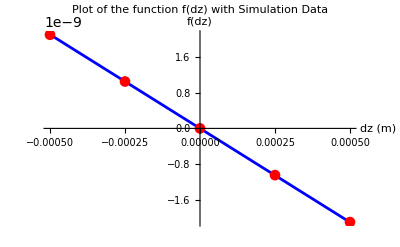

```mathematica
bz=3.3;
s=-0.1;
R=45.5*10^-6; (*converting micrometers to meters*)
μ=4*Pi*10^-7; (*You can replace this with the actual value of magnetic permeability*)
f[dz_]:=-(2 bz^2 dz π R^3 (5+9 s))/(5 μ)

(*Data points dz_Bz*)dataPoints={{500*10^-6,-2.0993669403968477*10^-9},{250*10^-6,-1.0472195538674522*10^-9},{0,1.11765177835113*10^-14},{-250*10^-6,1.0505799313730898*10^-9},{-500*10^-6,2.0983052443272467*10^-9}};


(*Plotting the function and the data points*)
plot1=Plot[f[dz],{dz,-500*10^-6,500*10^-6},PlotRange->All,AxesLabel->{"dz (m)","f(dz)"},PlotLabel->"Plot of the function f(dz) with Simulation Data",PlotStyle->Blue];

plot2=ListPlot[dataPoints,PlotStyle->{Red,PointSize[Medium]},PlotMarkers->Automatic];



(*Combining the plots with legends*)
Show[plot1,plot2,PlotLegends->{"Analytical Function","Simulation Result (y-component)","Simulation Result (z-component)"}]
```

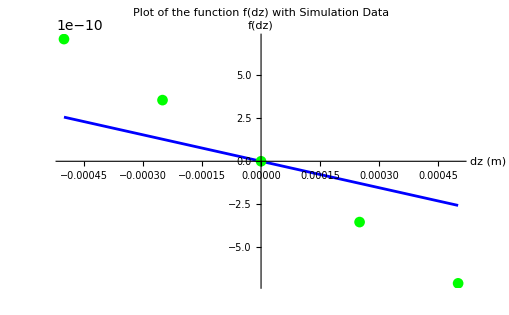

```mathematica
bz=3.3;
s=-0.5;
R=45.5*10^-6; (*converting micrometers to meters*)
μ=4*Pi*10^-7; (*You can replace this with the actual value of magnetic permeability*)
f[dz_]:=-(2 bz^2 dz π R^3 (5+9 s))/(5 μ)

(*Data points dz-Bz*)(*Second set of data points for z-component*)
dataPointsZ2={{500*10^-6,-7.089436370383137*10^-10},{250*10^-6,-3.531078639759586*10^-10},{0,4.02044242083225*10^-14},{-250*10^-6,3.5523812035263713*10^-10},{-500*10^-6,7.097431143372391*10^-10}};



(*Plotting the function and the data points*)
plot1=Plot[f[dz],{dz,-500*10^-6,500*10^-6},PlotRange->All,AxesLabel->{"dz (m)","f(dz)"},PlotLabel->"Plot of the function f(dz) with Simulation Data",PlotStyle->Blue];


plot3=ListPlot[dataPointsZ2,PlotStyle->{Green,PointSize[Medium]},PlotMarkers->Automatic];

(*Combining the plots with legends*)
Show[plot1,plot3,PlotLegends->{"Analytical Function","Simulation Result (y-component)","Simulation Result (z-component)"}]
```